# Plot-2D Graphics

Mathematica provides many functions to display data...

### Objectives

2D Plots

Plotting Numerical Data

Stylize Plots

#### Simple Example

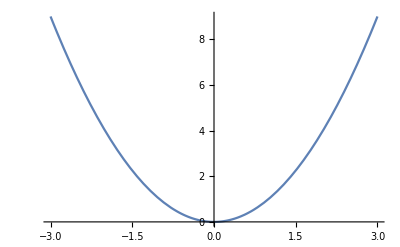

```mathematica
Plot[x^2,{x,-3,3}]
```

#### Multiple Functions

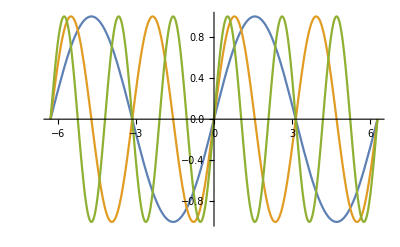

```mathematica
Plot[{Sin[x],Sin[2*x],Sin[3*x]}, {x,-2π,2π}]
```

#### Plot Range Option

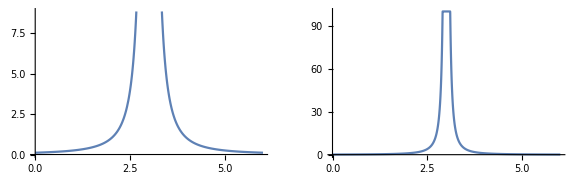

```mathematica
f[x_] := 1/(x-3)^2  /; x<2.9 || x>3.1
f[x_] := 100 /; 2.9  ≤ x ≤ 3.1
GraphicsRow[{Plot[f[x],{x,0,6}],Plot[f[x],{x,0,6},PlotRange->All]},ImageSize->Large]
```

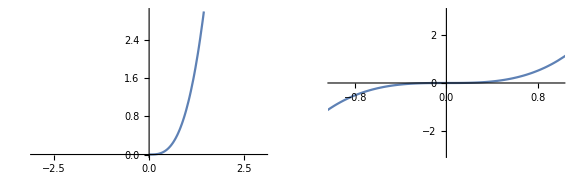

```mathematica
GraphicsRow[{Plot[x^3,{x,-3,3},PlotRange->{0,3}],Plot[x^3,{x,-3,3},PlotRange->{ {-1,1}, {-3,3} }]},ImageSize->Large]
```

#### Show Function

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

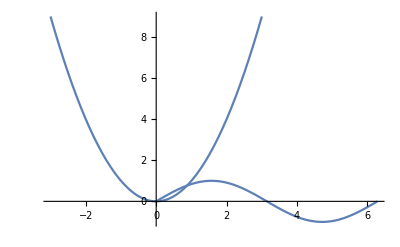

```mathematica
Show[{Plot[x^2,{x,-3,3}],Plot[Sin[x],{x,0,2π}]},PlotRange->All]
```

#### Graphics Grid

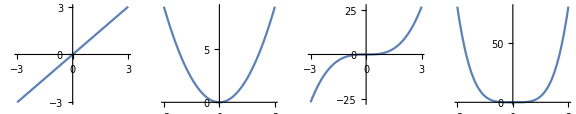

```mathematica
g1 = Plot[x,{x,-3,3}];
g2 = Plot[x^2,{x,-3,3}];
g3 = Plot[x^3,{x,-3,3}];
g4 = Plot[x^4,{x,-3,3}];
GraphicsGrid[{ {g1,g2,g3,g4}},ImageSize->Large]
```

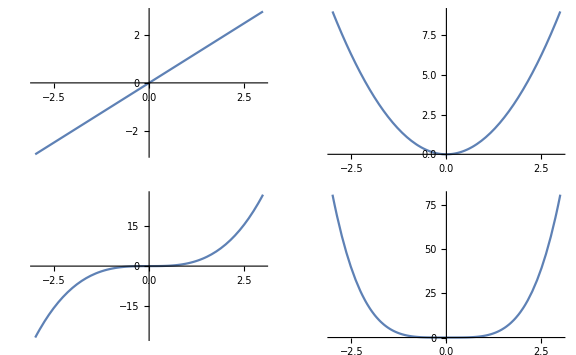

```mathematica
GraphicsGrid[{ {g1,g2}, {g3,g4}},ImageSize->Large]
```

#### Aspect Ratio Option

```mathematica
Plot[x^2,{x,-3,3}]
```

-Graphics-

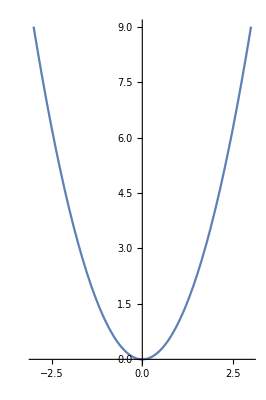

```mathematica
Plot[x^2,{x,-3,3},AspectRatio->Automatic]
```

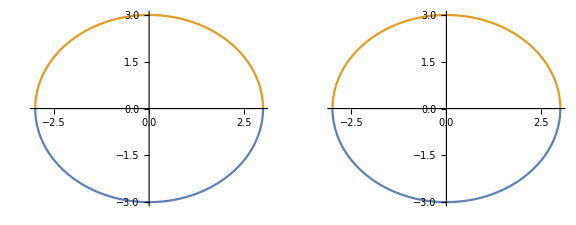

```mathematica
GraphicsGrid[{{ Plot[{-Sqrt[9-x^2],Sqrt[9-x^2]},{x,-3,3}],Plot[{-Sqrt[9-x^2],Sqrt[9-x^2]},{x,-3,3},AspectRatio->Automatic]}} ,ImageSize->Large]
```

### Styles

Red

White

Yellow

Purple

LightGray

LightBrown

Green

Gray

Brown

LightRed

LightCyan

LightOrange

Blue

Cyan

Orange

LightGreen

LightMagenta

LightPink

Black

Magenta

Pink

LightBlue

LightYellow

LightPurple

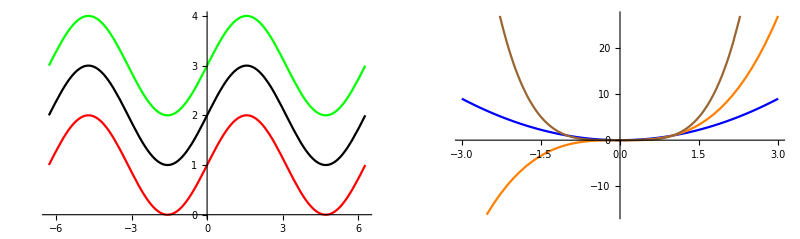

```mathematica
GraphicsGrid[{{Plot[{1+Sin[x],2+Sin[x],3+Sin[x]},{x,-2π,2π},PlotStyle->{Red,Black,Green}],Plot[{x^2,x^3,x^4},{x,-3,3},PlotStyle->{Blue,Orange,Brown}]}},ImageSize->Full]
```

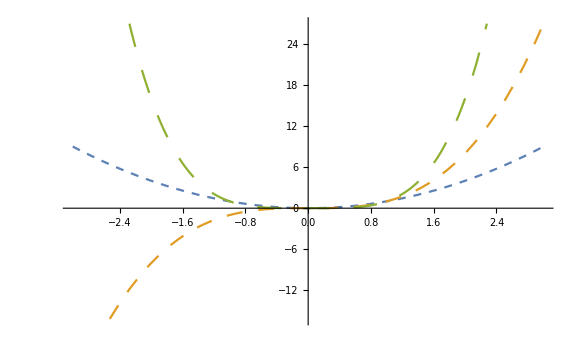

```mathematica
Plot[{x^2,x^3,x^4},{x,-3,3},PlotStyle->{Dashing[{0.01}],Dashing[{0.02}],Dashing[{0.03}]},ImageSize->Large]
```

### Plot Legends

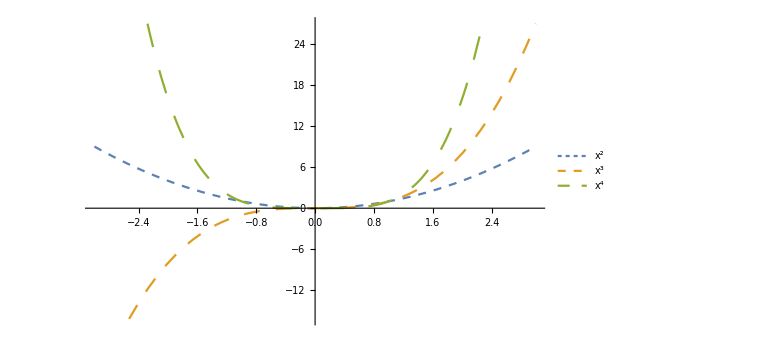

```mathematica
Plot[{x^2,x^3,x^4},{x,-3,3},PlotStyle->{Dashing[{0.01}],Dashing[{0.02}],Dashing[{0.03}]},ImageSize->Large,PlotLegends->"Expressions"]
```

```mathematica
Plot[{x^2,x^3,x^4},{x,-3,3},PlotStyle->{Dashing[{0.01}],Dashing[{0.02}],Dashing[{0.03}]},ImageSize->Large,
PlotLegends->Placed["Expressions",Below]]
```

-Graphics-

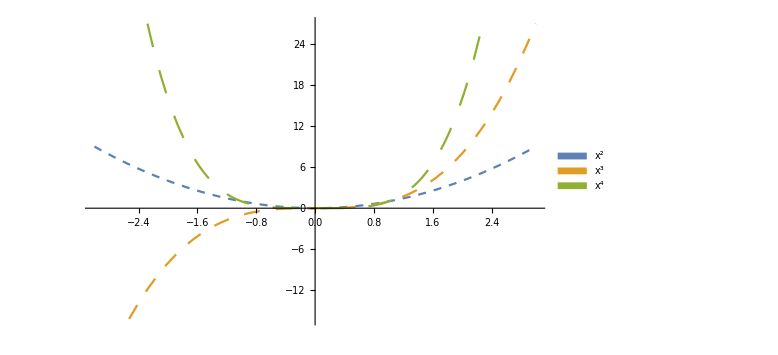

```mathematica
Plot[{x^2,x^3,x^4},{x,-3,3},PlotStyle->{Dashing[{0.01}],Dashing[{0.02}],Dashing[{0.03}]},ImageSize->Large,
PlotLegends->SwatchLegend["Expressions",LegendFunction->"Frame"]]
```

```mathematica
Plot[{x^2,x^3,x^4},{x,-3,3},PlotStyle->{Dashing[{0.01}],Dashing[{0.02}],Dashing[{0.03}]},ImageSize->Large,
PlotLegends->LineLegend["Expressions",LegendFunction->Framed]]
```

-Graphics-

```mathematica
Plot[{x^2,x^3,x^4},{x,-3,3},PlotStyle->{Dashing[{0.01}],Dashing[{0.02}],Dashing[{0.03}]},ImageSize->Large,
PlotLegends->Placed[SwatchLegend["Expressions",LegendFunction->"Frame"],Above]]
```

-Graphics-

### Plot Axes and Gridlines

```mathematica
f := 1/(x^2+1); 
g := x^2/(x^2+1);
```

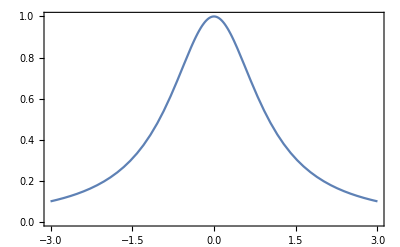

```mathematica
Plot[f,{x,-3,3},Frame->True,Axes->False]
```

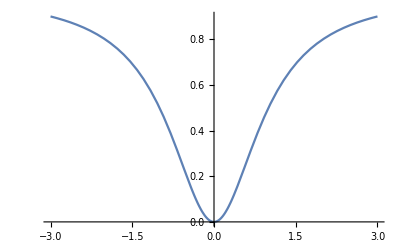

```mathematica
Plot[g,{x,-3,3},Ticks->None]
```

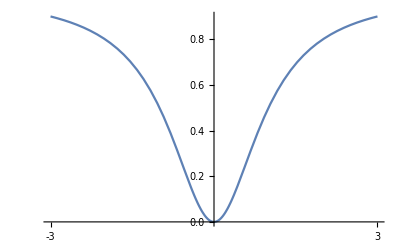

```mathematica
Plot[g,{x,-3,3},Ticks->{{-3,3},Automatic}]
```

### Plot Filling

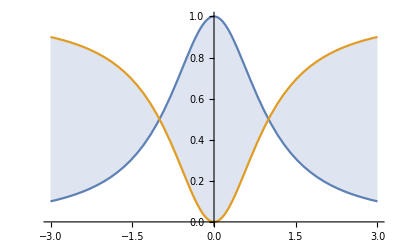

```mathematica
Plot[{f,g},{x,-3,3},Filling->{1->{2}}]
```

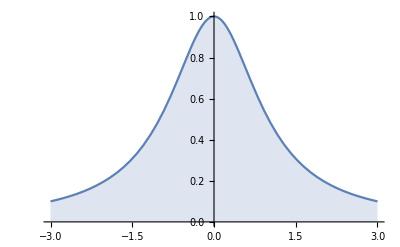

```mathematica
Plot[f,{x,-3,3},Filling-> Axis]
```

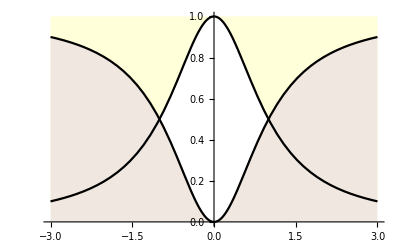

```mathematica
Plot[{f,g},{x,-3,3},PlotStyle->{Black,Black},Filling->{1->{Top,LightYellow},2 -> {Axis,LightBrown}},Ticks->{None,Automatic}]
```

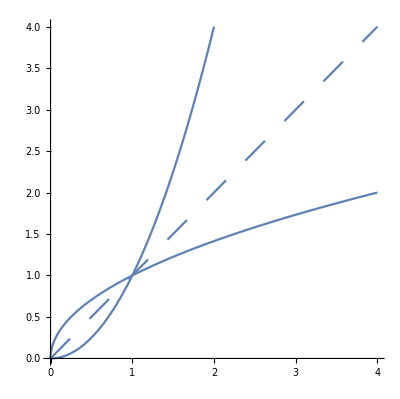

```mathematica
g1 := Plot[x^2,{x,0,2}];
g2 := Plot[Sqrt[x],{x,0,4}];
g3 := Plot[x,{x,0,4},PlotStyle->Dashing[{0.05}]];
Show[g1,g2,g3,AspectRatio->Automatic,PlotRange->{{0,4},Automatic}]
```

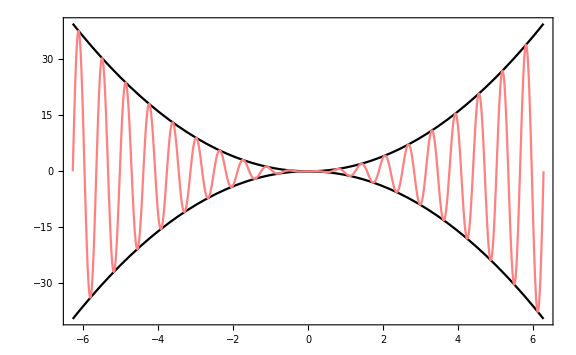

```mathematica
Plot[{x^2,-x^2,x^2*Sin[10x]},{x,-2π,2π},Frame->True,Ticks->{None,None},ImageSize->Large,PlotStyle->{Black,Black,Pink}]
```

```mathematica
TableForm[Table[{e,ChebyshevT[e,x]},{e,2,10}],TableHeadings->{None,{"Degree","ChebyshevT Polynomial"}},TableAlignments->Right]
```

Degree | ChebyshevT Polynomial
2 | -1+2 x^2
3 | -3 x+4 x^3
4 | 1-8 x^2+8 x^4
5 | 5 x-20 x^3+16 x^5
6 | -1+18 x^2-48 x^4+32 x^6
7 | -7 x+56 x^3-112 x^5+64 x^7
8 | 1-32 x^2+160 x^4-256 x^6+128 x^8
9 | 9 x-120 x^3+432 x^5-576 x^7+256 x^9
10 | -1+50 x^2-400 x^4+1120 x^6-1280 x^8+512 x^10

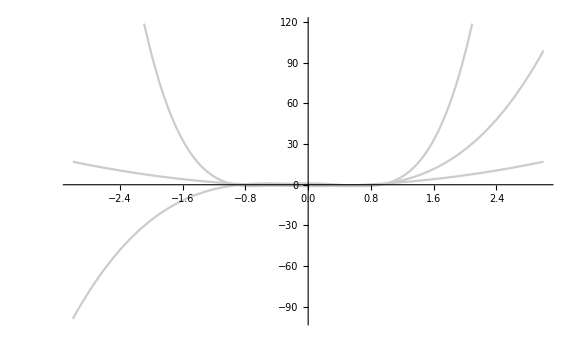

```mathematica
lst := Table[ChebyshevT[e,x],{e,2,4}]
Plot[lst,{x,-3,3},PlotStyle->{GrayLevel[.2],GrayLevel[.5],GrayLevel[.8]},ImageSize->Large,
PlotLegends->"Expressions"]
```